## Cold alkali-atom multi-channel scattering with Mathematica

See the notes “ScatteringTheoryNotes-NPM-2019.nb” for an earlier version of this scattering code with the theory background.  See “LiPotentials.nb” for the background on the hyperfine and Zeeman matrix elements and projection operators. Here, I’m copying over the relevant modules to have a more compact notebook with only the code, and minimal exposition.

```mathematica
invcminHartree = 4.5563352812122295*10^-6;
BohrinAngstrom=0.529177210903;
AngstrominBohr = 1/0.529177210903;
HartreePerMHz=6.579683920502*10^9;
MHzPerHartree = 1/HartreePerMHz;
nkinHartree=3.1668115634556 10^-15;
amu=(1.66053906660 10^-27)/(9.1093837015 10^-31);
mLi7=amu 7.01600455000;
μ=mLi7/2;
Off[ClebschGordan::phy]
Off[General::munfl]
```

### Morse/Long-Range Potential For Lithium (Coded by Alyson Laskowski, See Le Roy et al)

```mathematica
ypeq[p_,r_]:= (r^p - 1^p)/(r^p +1^p);
ypref[p_,r_]:= (r^p - 1.5^p)/(r^p +1.5^p);
DDS[r_,m_,bds_,cds_,ρ_,s_]:= (1-Exp[-(ρ r)(bds/m+(cds (ρ r))/m^(1/2))])^(m+s);
DTT[r_,m_,btt_,ρ_,s_]:= 1-Exp[-btt ρ r]*Sum[(btt ρ r)^k/(k!),{k,0,m-1+s}];
DDSTriplet[m_,r_]:= DDS[r,m,3.30,0.423,0.54,-1];
sde = 8516.7084;
tde = 333.758;
sre = 2.6729932;
tre = 4.17005000;
sref = 3.85;
tref = 8.0;
C6 = 6.71527 * 10^6;
C8 = 1.12588 * 10^8;
C10 = 2.78604 * 10^9;
tc6 = 6.7185*10^6;
tc8 =1.12629*10^8;
t10 = 2.78683*10^9;
p = 5;
q = 3;
ρ1 = 0.54;
sβcf1 = {-2.89828701, -1.309265,-2.018507, -1.38162,-1.21933, 0.3463, 0.1061,-0.1886,1.671,10.943,3.944,-27.23,-11.49,56.7, 38.9,-37.4, -33.0};
tβcf =  {-0.51608,-0.09782, 0.1137, -0.0248};
ulr[r_,dcf6_,dcf8_,dcf10_,c6_,c8_,c10_]:= dcf6 c6/r^6+dcf8 c8/r^8+dcf10 c10/r^10;
y[rp_,r_,p_]:=(r^p-rp^p)/(r^p+rp^p);
βinf[de_,re_,dcf6_,dcf8_,dcf10_,c6_,c8_,c10_]:= Log[(2 de)/ulr[re,dcf6,dcf8,dcf10,c6,c8,c10]];
βMLR[r_,βcf_,βinf_,ypeq_,ypref_,yqref_]:= βinf ypref+(1-ypref)* Sum[βcf[[j+1]]*(yqref)^j,{j,0,Length[βcf]-1}];
```

```mathematica
βinfT=βinf[tde,tre,DDSTriplet[6,tre],DDSTriplet[8,tre],DDSTriplet[10,tre],tc6,tc8,t10];
```

```mathematica
βTriplet[r_]:= βinfT*y[tref,r,5]+(1-y[tref,r,5])*Sum[tβcf[[j+1]]*y[tref,r,3]^j,{j,0,Length[tβcf]-1}];
ulrTriplet[r_]:= DDSTriplet[6,r] tc6/r^6+DDSTriplet[8,r] tc8/r^8+DDSTriplet[10,r] t10/r^10;
TripletMLR[r_]:= tde(1-ulrTriplet[r]/ulrTriplet[tre]*Exp[-βTriplet[r]*y[tre,r,p]])^2-tde;
```

```mathematica
VMLR[r_,re_,de_,β_,ypeq_,dcf6_,dcf8_,dcf10_,c6_,c8_,c10_]:= de(1-ulr[r,dcf6,dcf8,dcf10,c6,c8,c10]/ulr[re,dcf6,dcf8,dcf10,c6,c8,c10]*Exp[-β ypeq])^2-de;
SingletMLR[r_]:= VMLR[r,sre,sde,βMLR[r,sβcf1,βinf[sde,sre,1,1,1,C6,C8,C10],y[sre,r,p],y[sref,r,p],y[sref,r,q]],y[sre,r,p],1,1,1,C6,C8,C10]
```

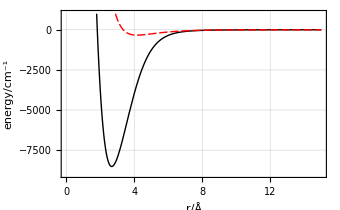

```mathematica
Plot[{SingletMLR[r],TripletMLR[r]},{r,1.5,15},Frame->True,FrameLabel->{"r/Å","energy/cm^-1"},PlotStyle->{{Black,Thick},{Red,Thick}},LabelStyle->Medium,GridLines->Automatic,PlotRange->{-9000,1000}]
```

#### Create an interpolated function to evaluate this fast and convert to van der Waals units

```mathematica
Rmax=300; (*bohr*)
Rmin=1.0;
NR =500;
dR=(Rmax-Rmin)/(NR-1);
RGrid =Table[Rmin+((iR-1)/(NR-1))^3(Rmax-Rmin),{iR,1,NR}];
```

```mathematica
TripletMLRHBdat = Table[{RGrid[[i]],invcminHartree*TripletMLR[RGrid[[i]]BohrinAngstrom]},{i,1,NR}];
TripletHBMLR=Interpolation[TripletMLRHBdat,Method->"Hermite",InterpolationOrder->5];
SingletMLRHBdat = Table[{RGrid[[i]],invcminHartree*SingletMLR[RGrid[[i]]BohrinAngstrom]},{i,1,NR}];
SingletHBMLR=Interpolation[SingletMLRHBdat,Method->"Hermite",InterpolationOrder->5];
```

General::munfl: Exp[-709.619] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-718.88] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-728.243] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

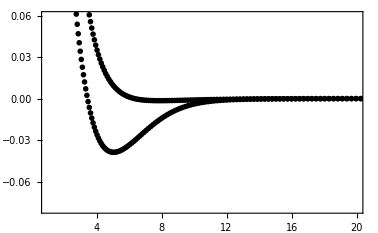

```mathematica
ListPlot[{SingletMLRHBdat,TripletMLRHBdat},PlotRange->{{Rmin,20},{-0.08,.06}},Frame->True]
```

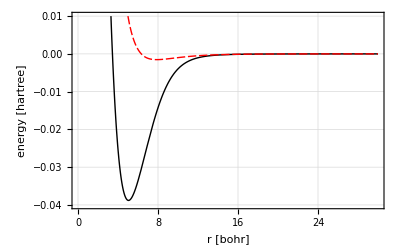

```mathematica
Plot[{SingletHBMLR[r],TripletHBMLR[r]},{r,Rmin,30},Frame->True,FrameLabel->{"r [bohr]","energy [hartree]"},PlotStyle->{{Black,Thick},{Red,Thick}},LabelStyle->Medium,GridLines->Automatic,PlotRange->{-0.04,0.01}]
```

```mathematica
Cvals={C6 invcminHartree AngstrominBohr^6,C8 invcminHartree AngstrominBohr^8,C10 invcminHartree AngstrominBohr^10}
```

{1393.39,83425.5,7.37211×10^6}

```mathematica
VLongRange[μ_,l_,Cvals_,r_]:=-Cvals[[1]]/r^6-Cvals[[2]]/r^8-Cvals[[3]]/r^10+(l(l+1))/(2μ r^2)
```

```mathematica
βvdw=r/.Simplify[Assuming[r>0,NSolve[VLongRange[μ,0,Cvals,r]==-1/(2μ r^2),r]]][[1]];
Evdw=1/(2μ βvdw^2);
Hartreeinvdw=1/Evdw;
bohrinvdw=1/βvdw;
C6OnlyVals={1,0,0};
```

These values are in atomic units.  Let’s compare them to the converted values used in the model.

```mathematica
Cvalsvdw={Cvals[[1]] bohrinvdw^6 Hartreeinvdw,Cvals[[2]] bohrinvdw^8 Hartreeinvdw,Cvals[[3]] bohrinvdw^10 Hartreeinvdw}
```

{0.985829,0.0138825,0.000288536}

```mathematica
RGridvdw=RGrid*bohrinvdw;
Tripletvdwdat = Table[{RGrid[[i]]bohrinvdw,Hartreeinvdw*invcminHartree*TripletMLR[RGrid[[i]]BohrinAngstrom]},{i,1,NR}];
TripletvdwMLR=Interpolation[Tripletvdwdat,Method->"Hermite",InterpolationOrder->5];
Singletvdwdat = Table[{RGrid[[i]]bohrinvdw,Hartreeinvdw invcminHartree*SingletMLR[RGrid[[i]]BohrinAngstrom]},{i,1,NR}];
SingletvdwMLR=Interpolation[Singletvdwdat,Method->"Hermite",InterpolationOrder->5];
```

General::munfl: Exp[-709.619] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-718.88] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-728.243] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
7/βvdw
```

0.107354

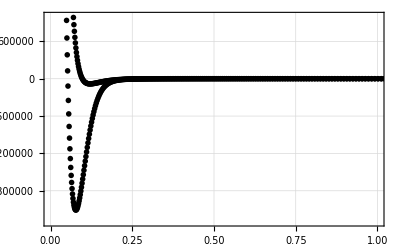

```mathematica
ListPlot[{Singletvdwdat,Tripletvdwdat},PlotRange->(*{{0.0,50},{-0.04,0.01}}*){{0,1},{-2.3 10^6,10^6}},Frame->True,GridLines->Automatic,GridLinesStyle->Thin]
```

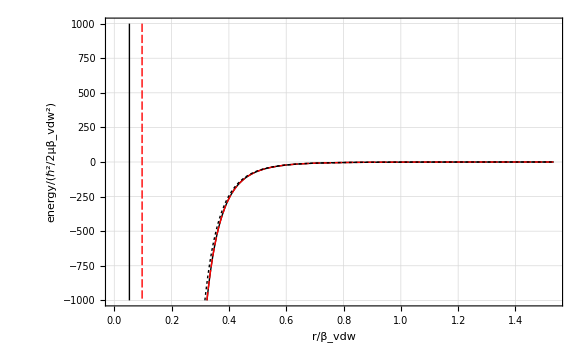

```mathematica
Plot[{SingletvdwMLR[r],TripletvdwMLR[r],VLongRange[1/2,0,C6OnlyVals,r]},{r,RGridvdw[[1]],RGridvdw[[NR]]/3},Frame->True,FrameLabel->{"r/β_vdw","energy/(ℏ^2/2μβ_vdw^2)"},PlotStyle->{{Black,Thick},{Red,Thick}},LabelStyle->Medium,GridLines->Automatic,PlotRange->{-1000,1000}]
```

### Standardization of Milne reference functions

```mathematica
FullSimplify[D[χminus[L,r],r]]
```

(-L r^2 BesselJ[1/4 (1+2 L),1/(2 r^2)]+BesselJ[1/4 (5+2 L),1/(2 r^2)])/r^(5/2)

```mathematica
FullSimplify[D[χplus[L,r],r]]
```

((1+L) r^2 BesselJ[1/4 (-1-2 L),1/(2 r^2)]+BesselJ[1/4 (3-2 L),1/(2 r^2)])/r^(5/2)

```mathematica
Lmax=4;
χplus[L_,R_]:=√R BesselJ[-1/4(2L+1),1/(2 R^2)];
χminus[L_,R_]:=√R BesselJ[1/4(2L+1),1/(2 R^2)];
χmprime[L_,r_]:=(-L r^2 BesselJ[1/4 (1+2 L),1/(2 r^2)]+BesselJ[1/4 (5+2 L),1/(2 r^2)])/r^(5/2);
χpprime[L_,r_]:=((1+L) r^2 BesselJ[1/4 (-1-2 L),1/(2 r^2)]+BesselJ[1/4 (3-2 L),1/(2 r^2)])/r^(5/2);
ksqr[ϵ_,l_,r_]:=ϵ-VLongRange[1/2,l,Cvalsvdw,r];
BC1[ϵ_,l_,r_]=Simplify[Evaluate[(ksqr[ϵ,l,r])^(-1/4)]];
BC2[ϵ_,l_,r_]=Simplify[Evaluate[D[(ksqr[ϵ,l,r])^(-1/4),r]]];
```

```mathematica
ϵtest=0.0;
rx=0.1;
rf=3.0;
nr=300;
```

```mathematica
αsol=Flatten[Table[NDSolve[{α''[r]+ksqr[ϵtest,l,r]α[r]-1/α[r]^3==0,α[rx]==BC1[ϵtest,l,rx],α'[rx]==BC2[ϵtest,l,rx]},α,{r,rx,rf}],{l,0,Lmax}]];
```

```mathematica
αfun=Table[α/.αsol[[i]],{i,1,Length[αsol]}];
```

```mathematica
rGrid=Table[rx+((i-1)/(nr-1))^3(rf-rx),{i,1,nr}];
```

```mathematica
PhaseIntTable=Table[Flatten[{0,Table[NIntegrate[(αfun[[ltest+1]][rp])^-2/.αsol,{rp,rGrid[[i-1]],rGrid[[i]]}],{i,2,nr}]}],{ltest,0,Lmax}];
```

```mathematica
phaseintfun=Table[Interpolation[Table[{rGrid[[i]],Total[PhaseIntTable[[ltest+1,1;;i]]]},{i,1,nr}]],{ltest,0,Lmax}];
```

Now using (ⅆf^0(r))/ⅆr=(α'(r))/(α(r))f^0(r)-1/(α^2(r)) g^0(r)
(ⅆg^0(r))/ⅆr=(α'(r))/(α(r))g^0(r)+1/(α^2(r)) f^0(r)

```mathematica
basepairs[l_,ϕ_,α_,phaseint_,r_]:=Module[{αp,rp,f0,g0,f0p,g0p,χm,χmp},
αp=D[α[rp],rp]/.rp->r;
g0=(-α[r])/(√π)Cos[ϕ+phaseint[r]];
f0=α[r]/(√π)Sin[ϕ+phaseint[r]];
f0p=αp/α[r] f0-1/α[r]^2 g0;
g0p=αp/α[r] g0+1/α[r]^2 f0;
χm=χminus[l,r];
χmp=χmprime[l,r];
{f0,g0,f0p,g0p,χm,χmp}]
```

```mathematica
tanphi=Table[{f0,g0,f0p,g0p,χm,χmp}=basepairs[ltest,0.0,αfun[[ltest+1]],phaseintfun[[ltest+1]],rf];-(χm g0p-χmp g0)/(χm f0p-χmp f0),{ltest,0,Lmax}]
```

{0.99335,39.2781,-1.13452,-0.114651,0.695132}

```mathematica
Table[Tan[-1/(2 rx^2)+(L π)/4-(5π)/8],{L,0,Lmax}]
```

{7.81816,-1.29333,-0.127907,0.773195,7.81816}

```mathematica
ϕvals=ArcTan[tanphi]
```

{0.782062,1.54534,-0.848334,-0.114152,0.607451}

```mathematica
g0function[ϕ_,α_,phaseintfun_,r_]:=(-α[r])/(√π)Cos[ϕ+phaseintfun[r]]
f0function[ϕ_,α_,phaseintfun_,r_]:=α[r]/(√π)Sin[ϕ+phaseintfun[r]]
```

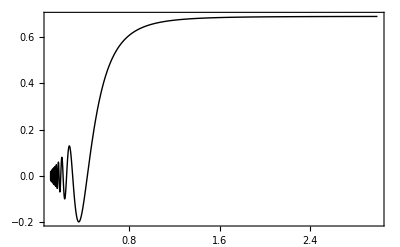

```mathematica
ltest=0;Plot[g0function[ϕvals[[ltest+1]],αfun[[ltest+1]],phaseintfun[[ltest+1]],r],{r,rx,rf},PlotRange->All,PlotStyle->{Black,Thin},Frame->True]
```

### Find the singlet/triplet quantum defects

```mathematica
CalcY[Ε_,l_,rmin_,rmax_,μ_,r0_,U_]:=Module[{Y,u,up,rp,r},
u=NDSolveValue[{-1/(2 μ)u''[r]+ (U[r]+(l(l+1))/(2 μ r^2))*u[r]==Ε u[r],u[rmin]==0,u'[rmin]==10^-10},u,{r,rmin,rmax},AccuracyGoal->20];
up[r_] = D[u[rp],rp]/.rp->r;
Y = up[r]/u[r]/.r->r0;
Return[{Y,u}]
]
```

```mathematica
QuantumDefect[ϕ_,l_,rmin_,rx_,r0_,rmax_,U_,ϵ_,μ_]:=Module[{u,α,rp,αrule,αfun,phaseint,f0,g0,f0p,g0p,αp,χm,χmp,logder,Ksr},
αrule=NDSolve[{α''[r]+ksqr[ϵ,l,r]α[r]-1/α[r]^3==0,α[rx]==BC1[ϵ,l,rx],α'[rx]==BC2[ϵ,l,rx]},α,{r,rx,rmax},AccuracyGoal->20];
αfun=α/.αrule[[1]];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,r0}];
αp=D[αfun[rp],rp]/.rp->r0;
g0=(-αfun[r0])/(√π)Cos[ϕ+phaseint];
g0p=αp/αfun[r0] g0+1/αfun[r0]^2 f0;
f0=αfun[r0]/(√π)Sin[ϕ+phaseint];
f0p=αp/αfun[r0] f0-1/αfun[r0]^2 g0;
{logder,u}=CalcY[ϵ,l,rmin,rmax,μ,r0,U];
Ksr=(logder f0-f0p)/(logder g0-g0p);
{Ksr,ArcTan[Ksr]/π}
]
```

```mathematica
rmin=2.0/βvdw;
rmax =3.0;
rx=0.1;
Εtest=0.0;
r0=40/βvdw;
ltest=0;
μtableT3=Table[{Εtest,QuantumDefect[ϕvals[[ltest+1]],ltest,rmin,rx,r0,rmax,TripletvdwMLR,Εtest,1/2][[2]]},{Εtest,-100,100,5}];
μtableS3=Table[{Εtest,QuantumDefect[ϕvals[[ltest+1]],ltest,rmin,rx,r0,rmax,SingletvdwMLR,Εtest,1/2][[2]]},{Εtest,-100,100,5}];
pμ3=ListPlot[{μtableT3,μtableS3},PlotStyle->{Green},PlotMarkers->None,Joined->True];
```

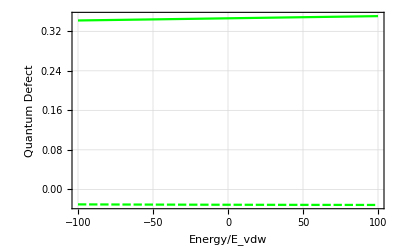

```mathematica
Show[pμ3,Frame->True,GridLines->Automatic,GridLinesStyle->Thin,FrameLabel->{"Energy/E_vdw","Quantum Defect"}]
```

```mathematica
μS=Interpolation[μtableS3];
μT=Interpolation[μtableT3];
```

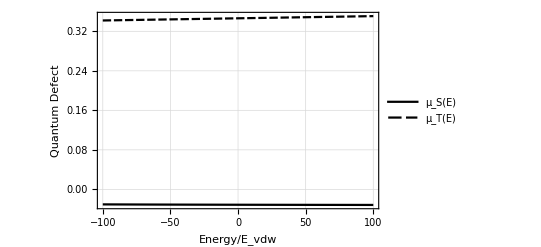

```mathematica
Plot[{Legended[μS[EE],"μ_S(E)"],Legended[μT[EE],"μ_T(E)"]},{EE,-100,100},Frame->True,GridLines->Automatic,GridLinesStyle->Thin,FrameLabel->{"Energy/E_vdw","Quantum Defect"}]
```

### Hyperfine & Zeeman Matrix Elements

H = -ℏ^2/(2 μ) d^2/(d r^2) + P_0 V_0(r) + P_1 V_1(r) +(l(l+1)ℏ^2)/(2 μ r^2)+ ∑A_i(s_i· i_i) + (g_s^(i) μ_B s_z^(i)+ g_i^(i)μ_N i_z^(i))B

```mathematica
Li7s = 1/2;
Li7i = 3/2;
Li7gs = 2.0;
Li7gi = 2.170903;
Li6s = Li7s;
Li6i = 1;
Li6gs = Li7gs;
Li6gi = 0.822019;
Li7AH =401.7520435*MHzPerHartree Hartreeinvdw; (*MHz -> Hartree -> vdW units*)
Li6AH = 152.136840720*MHzPerHartree Hartreeinvdw;  (*MHz -> Hartree*)
μbH = 1.3996244936142*MHzPerHartree Hartreeinvdw;   (*MHz/G  ->  Hartree/G -> Subscript[E, vdW]/G*)
μnH = 7.62259328547*10^-4*MHzPerHartree Hartreeinvdw;(* MHz/G -> Hartree/G -> Subscript[E, vdW]/G *)
```

```mathematica
f1m1f2m2basis=Sort[Flatten[Table[Table[{f1,m1, f2, m2},{m1,-f1,f1},{m2,-f2,f2}],{f1,1,2},{f2,1,2}],3]];
```

For M_T=2

Unsymmetrized Basis

```mathematica
mF2unsym =Select[f1m1f2m2basis,#[[2]]+#[[4]]==2&]
```

{{1,0,2,2},{1,1,1,1},{1,1,2,1},{2,0,2,2},{2,1,1,1},{2,1,2,1},{2,2,1,0},{2,2,2,0}}

```mathematica
mF2basis = {{1,0,2,2},{1,1,1,1},{1,1,2,1},{2,0,2,2},{2,1,2,1}};
```

Use the following line and skip the lengthy projection operator calculation if you only want Li-7 M_F=2.

```mathematica
SymSingletProjLi7MF2={{1/4,-(√3)/8,-1/(4 √2),-1/4,(√3)/8},{-(√3)/8,3/16,(√(3/2))/8,(√3)/8,-3/16},{-1/(4 √2),(√(3/2))/8,1/8,1/(4 √2),-(√(3/2))/8},{-1/4,(√3)/8,1/(4 √2),1/4,-(√3)/8},{(√3)/8,-3/16,-(√(3/2))/8,-(√3)/8,3/16}};
SymTripletProjLi7MF2={{3/4,(√3)/8,1/(4 √2),1/4,-(√3)/8},{(√3)/8,13/16,-(√(3/2))/8,-(√3)/8,3/16},{1/(4 √2),-(√(3/2))/8,7/8,-1/(4 √2),(√(3/2))/8},{1/4,-(√3)/8,-1/(4 √2),3/4,(√3)/8},{-(√3)/8,3/16,(√(3/2))/8,(√3)/8,13/16}};
```

### Uncomment all of this stuff below if you want to calculate the projection operators from scratch -- but this takes a long time, and I’ve hard-coded them above.

```mathematica
(*ProjectionCoefficient[f1_,m1_,f2_,m2_,s_,ms_,i_,mi_,s1_,i1_,s2_,i2_]:= (-1)^(2i2-2s1-m1-m2-ms-mi)√((2f1+1)(2f2+1)(2s+1)(2i+1)) Sum[ThreeJSymbol[{s1,ms1},{i1,mi1},{f1, -m1}]*ThreeJSymbol[{s2,ms2},{i2,mi2},{f2,-m2}]*ThreeJSymbol[{s1,ms1},{s2,ms2},{s,-ms}]*ThreeJSymbol[{i1,mi1},{i2,mi2},{i,-mi}],{ms1,-s1,s1},{mi1,-i1,i1},{ms2,-s2,s2},{mi2,-i2,i2}];*)

(*ProjectionMatrixElement[f1_,m1_,f1p_,m1p_,f2_,m2_,f2p_,m2p_,s1_,i1_,s2_,i2_,S_]:= Sum[Sum[ProjectionCoefficient[f1,m1,f2,m2,s,ms,i,mi,s1,i1,s2,i2]*ProjectionCoefficient[f1p,m1p,f2p,m2p,s,ms,i,mi,s1,i1,s2,i2]*KroneckerDelta[s,S],{ms,-s,s},{mi,-i,i}],{s,Abs[s1-s2],Abs[s1+s2]},{i,Abs[i1-i2],Abs[i1+i2]}];*)
```

```mathematica
(*SingletProjectionMatrix= Table[Sum[Sum[ProjectionCoefficient[mF2unsym[[j,1]],mF2unsym[[j,2]],mF2unsym[[j,3]],mF2unsym[[j,4]],s,ms,i,mi,Li7s,Li7i,Li7s,Li7i]*ProjectionCoefficient[mF2unsym[[jp,1]],mF2unsym[[jp,2]],mF2unsym[[jp,3]],mF2unsym[[jp,4]],s,ms,i,mi,Li7s,Li7i,Li7s,Li7i] *KroneckerDelta[s,0],{ms,-s,s},{mi,-i,i}],{s,0,1},{i,0,3}],{j,1,8},{jp,1,8}];*)
```

```mathematica
(*SingletProjectionSym[p_,l_]:= Table[(1/(2√((1+KroneckerDelta[mF2basis[[j,1]],mF2basis[[j,3]]] KroneckerDelta[mF2basis[[j,2]],mF2basis[[j,4]]])(1+KroneckerDelta[mF2basis[[jp,1]],mF2basis[[jp,3]]] KroneckerDelta[mF2basis[[jp,2]],mF2basis[[jp,4]]]))))*(ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7s,Li7i,0]+ProjectionMatrixElement[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7s,Li7i,0]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7s,Li7i,0]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7s,Li7i,0]),{j,1,5},{jp,1,5}]*)
```

```mathematica
(*SProjSymLi7=FullSimplify[SingletProjectionSym[0,0]]*)
```

```mathematica
(*TripletProjectionMatrix = Table[Sum[Sum[ProjectionCoefficient[mF2unsym[[j,1]],mF2unsym[[j,2]],mF2unsym[[j,3]],mF2unsym[[j,4]],s,ms,i,mi,Li7s,Li7i,Li7s,Li7i]*ProjectionCoefficient[mF2unsym[[jp,1]],mF2unsym[[jp,2]],mF2unsym[[jp,3]],mF2unsym[[jp,4]],s,ms,i,mi,Li7s,Li7i,Li7s,Li7i]* KroneckerDelta[s,1],{ms,-s,s},{mi,-i,i}],{s,0,1},{i,0,3}],{j,1,8},{jp,1,8}];*)
```

For symmetrized basis:

```mathematica
(*TripletProjectSym[p_,l_]:=Table[(1/(2√((1+KroneckerDelta[mF2basis[[j,1]],mF2basis[[j,3]]] KroneckerDelta[mF2basis[[j,2]],mF2basis[[j,4]]])(1+KroneckerDelta[mF2basis[[jp,1]],mF2basis[[jp,3]]] KroneckerDelta[mF2basis[[jp,2]],mF2basis[[jp,4]]]))))*(ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7s,Li7i,1]+ProjectionMatrixElement[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7s,Li7i,1]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7s,Li7i,1]+ (-1)^p(-1)^l ProjectionMatrixElement[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7s,Li7i,1]),{j,1,5},{jp,1,5}] *)
```

```mathematica
(*TProjSymLi7=FullSimplify[TripletProjectSym[0,0]];*)
```

```mathematica
(*TProjSymLi7*)
```

```mathematica
(*MatrixForm[N[TProjSymLi7]]*)
```

(s i)f'm' H^HZ(s i)f m=A^HF/2[f(f+1)-s(s+1)-i(i+1)]δ_ff' δ_mm'+g_s μ_B B√(2f'+1)(2f+1) ∑_(m_s,m_i) m_s(s | i
m_s | m_i f'
-m')(s | i
m_s | m_i f
-m)δ_mm'+g_i μ_N B√(2f'+1)(2f+1) ∑_(m_s,m_i) m_i(s | i
m_s | m_i f'
-m')(s | i
m_s | m_i f
-m)δ_mm'

```mathematica
HZ[f_,m_,fp_,mp_,s_,i_,gs_,gi_,A_,B_]:= A/2(f(f+1)-i(i+1)-s(s+1))KroneckerDelta[f,fp] KroneckerDelta[m,mp]+gs μbH B √((2fp+1)(2f+1))Sum[ms ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp]+gi μnH B √((2fp+1)(2f+1))Sum[mi ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp];
```

McAlexander Eq. E.5 (for symmetrized basis)

{α'β'}H_1^HZ+H_2^HZ{αβ}=1/(√((1+δ_α)(1+δ_α'β')))[α' H^HZ α δ_ββ'+β' H^HZ β δ_αα'±(-1)^l α' H^HZ β δ_αβ'±(-1)^l β' H^HZ α δ_βα']

```mathematica
HZsym[p_,l_,B_]:=Table[(1/(√((1+KroneckerDelta[mF2basis[[j,1]],mF2basis[[j,3]]] KroneckerDelta[mF2basis[[j,2]],mF2basis[[j,4]]])(1+KroneckerDelta[mF2basis[[jp,1]],mF2basis[[jp,3]]] KroneckerDelta[mF2basis[[jp,2]],mF2basis[[jp,4]]]))))*(HZ[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]KroneckerDelta[mF2basis[[j,3]],mF2basis[[jp,3]]]KroneckerDelta[mF2basis[[j,4]],mF2basis[[jp,4]]]+HZ[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]KroneckerDelta[mF2basis[[j,1]],mF2basis[[jp,1]]]KroneckerDelta[mF2basis[[j,2]],mF2basis[[jp,2]]]+(-1)^p(-1)^l HZ[mF2basis[[j,3]],mF2basis[[j,4]],mF2basis[[jp,1]],mF2basis[[jp,2]],Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]KroneckerDelta[mF2basis[[j,1]],mF2basis[[jp,3]]]KroneckerDelta[mF2basis[[j,2]],mF2basis[[jp,4]]]+(-1)^p(-1)^l HZ[mF2basis[[j,1]],mF2basis[[j,2]],mF2basis[[jp,3]],mF2basis[[jp,4]],Li7s,Li7i,Li7gs,Li7gi,Li7AH,B]KroneckerDelta[mF2basis[[j,3]],mF2basis[[jp,1]]]KroneckerDelta[mF2basis[[j,4]],mF2basis[[jp,2]]]),{j,1,5},{jp,1,5}]
```

```mathematica
Eigensystem[FullSimplify[HZsym[0,0,B]]/.B->0][[1]]
```

{-8.30048,4.98029,4.98029,-1.6601,-1.6601}

```mathematica
HZsymLi7[B_]=FullSimplify[HZsym[0,0,B]];
```

```mathematica
Htest[r_,B_]:= HZsymLi7[B]+SymTripletProjLi7MF2*TripletvdwMLR[r]+SymSingletProjLi7MF2*SingletvdwMLR[r];
```

```mathematica
ValVecs[B_]:=Table[ Sort[Transpose[Eigensystem[Htest[RGridvdw[[iR]],B]]]],{iR,1,NR}];
```

```mathematica
NR
```

500

```mathematica
AdiabaticUV=Table[{{RGridvdw[[iR]],ValVecs[0.0][[iR,n,1]]},ValVecs[0.0][[iR,n,2]]},{iR,1,NR,5},{n,1,5}];
```

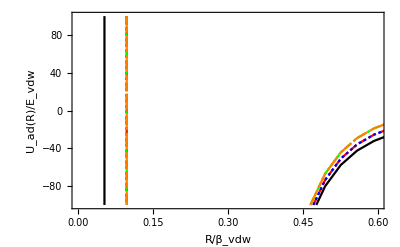

```mathematica
padiabatic=ListPlot[Table[AdiabaticUV[[1;;Length[AdiabaticUV],n,1]],{n,1,5}],Joined->True,PlotMarkers->None,Frame->True,PlotRange->{{0,.6},{-1 10^2,10^2}},PlotStyle->{Black,Red,Blue,Green,Orange},FrameLabel->{"R/β_vdw","U_ad(R)/E_vdw"}]
```

```mathematica
AsymC[B_]:=Transpose[Sort[Transpose[Eigensystem[HZsymLi7[B]]]]][[2]];
Eth[B_]:=Transpose[Sort[Transpose[Eigensystem[HZsymLi7[B]]]]][[1]];
```

```mathematica
EthA=Table[Interpolation[Table[{B,Eth[B][[n]]},{B,0,1200,0.5}],InterpolationOrder->1],{n,1,5}]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

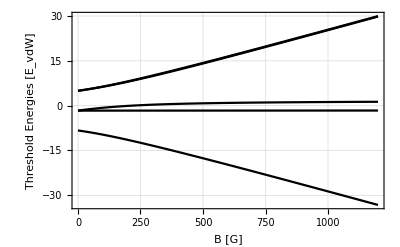

```mathematica
Plot[Table[EthA[[n]][B],{n,1,5}],{B,0,1200},PlotRange->All,Frame->True,GridLines->{Automatic},GridLinesStyle->Directive[Thin] ,FrameLabel->{"B [G]","Threshold Energies [E_vdW]"}]
```

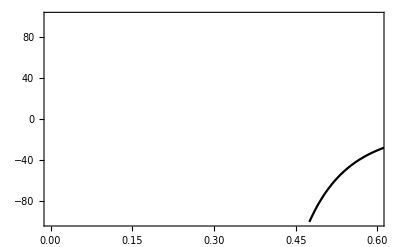

```mathematica
plr=Plot[EthA[[1]][0]+VLongRange[1/2,0,Cvalsvdw,r],{r,rmin,rmax},Frame->True,PlotRange->{{0,0.6},{-1 10^2,10^2}}]
```

```mathematica
(*Show[padiabatic,plr]*)
```

```mathematica
Wronskian[{ r SphericalBesselJ[l,k r], r SphericalBesselY[l,k r]},r]
```

1/k

### Find all of the MQDT parameters as a function of energy

```mathematica
QuantumDefectParameters[ϕ_,l_,rx_,rfinal_,ϵ_]:=Module[{fs,fsp,gs,gsp,𝒜,𝒢,tanη,k,α,rp,αrule,αfun,phaseint,f0,g0,f0p,g0p,αp,χm,χmp,γ,Ksr,Wfsgs,Wfsf0,Wfsg0,Wgsg0,Wgsf0},
(*rx=0.1;*)
k=√ϵ;
fs=(*√(k/π)*) rfinal SphericalBesselJ[l,k rfinal];
fsp=D[(*√(k/π)*)rp SphericalBesselJ[l,k rp],rp]/.rp->rfinal;
gs=(*√(k/π)*) rfinal  SphericalBesselY[l,k rfinal];
gsp=D[ (*√(k/π)*)rp SphericalBesselY[l,k rp],rp]/.rp->rfinal;
αrule=NDSolve[{α''[r]+ksqr[ϵ,l,r]α[r]-1/α[r]^3==0,α[rx]==BC1[ϵ,l,rx],α'[rx]==BC2[ϵ,l,rx]},α,{r,rx,rfinal}];
αfun=α/.αrule[[1]];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rfinal}];
αp=D[αfun[rp],rp]/.rp->rfinal;
g0=(-αfun[rfinal])/(√π)Cos[ϕ+phaseint];
f0=αfun[rfinal]/(√π)Sin[ϕ+phaseint];
f0p=αp/αfun[rfinal] f0-1/αfun[rfinal]^2 g0;
g0p=αp/αfun[rfinal] g0+1/αfun[rfinal]^2 f0;
Wfsf0=fs f0p - fsp f0;
Wgsf0=gs f0p - gsp f0;
Wfsg0=fs g0p-fsp g0;
Wgsg0=gs g0p-gsp g0;
Wfsgs=fs gsp-fsp gs;
tanη=Wfsf0/Wgsf0;

(*𝒜=(Wfsgs^2(*k*))/(Wfsf0^2+Wgsf0^2);*)
𝒜=(tanη Wgsg0 -Wfsg0)/(tanη Wfsf0 +Wgsf0);
𝒢=-(Wfsg0*Wfsf0+Wgsg0*Wgsf0)/(Wfsf0^2+Wgsf0^2);

{tanη,𝒜,𝒢}
]
```

```mathematica
QuantumDefectParametersBound[ϕ_,l_,rx_,rfinal_,ϵ_]:=Module[{tanγ,gbound,gboundp,k,κ,α,rp,αrule,αfun,phaseint,f0,g0,f0p,g0p,αp,γ},
k=√ϵ;
κ=√-ϵ;
gbound=√(2/π κ rp) BesselK[l+1/2,κ rp]/.rp->rfinal;
gboundp=D[√(2/π κ rp) BesselK[l+1/2,κ rp],rp]/.rp->rfinal;
αrule=NDSolve[{α''[r]+ksqr[ϵ,l,r]α[r]-1/α[r]^3==0,α[rx]==BC1[ϵ,l,rx],α'[rx]==BC2[ϵ,l,rx]},α,{r,rx,rfinal}];
αfun=α/.αrule[[1]];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rfinal}];
αp=D[αfun[rp],rp]/.rp->rfinal;
g0=-αfun[rfinal]Cos[ϕ+phaseint];
f0=αfun[rfinal]Sin[ϕ+phaseint];
f0p=αp/αfun[rfinal] f0-1/αfun[rfinal]^2 g0;
g0p=αp/αfun[rfinal] g0+1/αfun[rfinal]^2 f0;
tanγ=-(gbound g0p-gboundp g0)/(gbound f0p - gboundp f0);
{tanγ}
]
```

```mathematica
NE=100;ϵ0=10^-14;ϵf=60;
ϵtable=Table[ϵ0+((i-1)/(NE-1))^3(ϵf-ϵ0),{i,1,NE}];
```

```mathematica
γ0table=Sort[Table[{ϵ,ArcTan[QuantumDefectParametersBound[ϕvals[[ltest+1]],ltest,rx,rf,ϵ][[1]]]},{ϵ,-ϵtable}]];
```

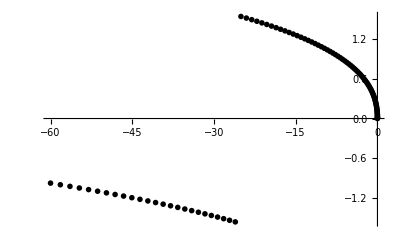

```mathematica
ListPlot[γ0table]
```

26

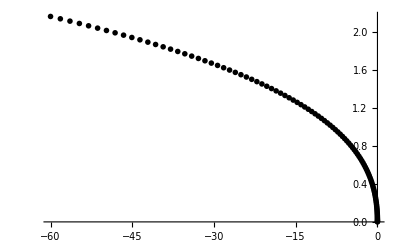

```mathematica
γ0tablenew=γ0table;
For[i=Length[γ0table],i>1,i--,
If[(γ0table[[i-1,2]]-γ0table[[i,2]]<-1.2),Print[i];
γ0tablenew[[1;;i-1,2]]=γ0tablenew[[1;;i-1,2]]+π,γ0tablenew[[1;;i-1,2]]=γ0tablenew[[1;;i-1,2]]]
]
ListPlot[γ0tablenew]
```

```mathematica
γfun=Interpolation[γ0tablenew,InterpolationOrder->1]
```

InterpolatingFunction[…]

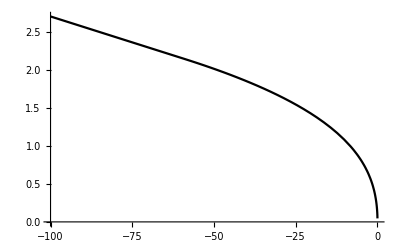

```mathematica
Plot[γfun[EE],{EE,-100,-0.01}]
```

```mathematica
ltest=0;
lowEparameters=Table[QuantumDefectParameters[ϕvals[[ltest+1]],ltest,rx,rf,ϵtable[[i]]],{i,1,NE}];
```

51

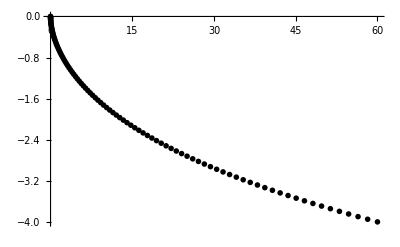

```mathematica
ηtable=Table[{ϵtable[[i]],ArcTan[lowEparameters[[i,1]]]},{i,1,NE}];
ηtablenew=ηtable;
For[i=1,i<Length[ηtable],i++,
If[(ηtable[[i+1,2]]-ηtable[[i,2]]>1.2),Print[i];
ηtablenew[[i+1;;NE,2]]=ηtablenew[[i+1;;NE,2]]-π,ηtablenew[[i+1;;NE,2]]=ηtablenew[[i+1;;NE,2]]
]];
peta1=ListPlot[ηtablenew]
(*ListPlot[ηtable]*)
```

```mathematica
ηfun=Interpolation[ηtablenew,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
abar[L_]:=((π 2^(-(2L+3/2)))/(Gamma[L/2+5/4]Gamma[L+1/2]))^(2/(2L+1))
```

```mathematica
ηlowE[ϵ_,L_]:=(-1)^(L+1)(abar[L] √ϵ)^(2L+1)-(3π Gamma[L-3/2])/(32 Gamma[L+7/2])ϵ^2
```

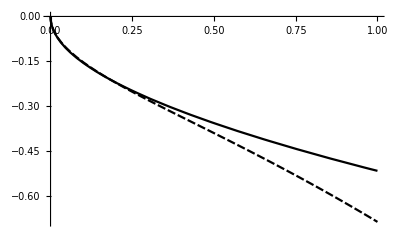

```mathematica
peta2=Plot[{ηfun[ϵ],ηlowE[ϵ,0]},{ϵ,0,1}]
```

```mathematica
(abar[0] √ϵ)^(1/2)
```

(√π ϵ^(1/4))/(2 √2 Gamma[5/4])

```mathematica
Ahalfdat=Table[{ϵtable[[i]],-√lowEparameters[[i,2]]},{i,1,NE}];
Ahalfplot1=ListPlot[Ahalfdat,PlotStyle->Black,Joined->True,PlotMarkers->None];
Ahalfplot2=Plot[-(abar[L] √ϵ)^(L+1/2)/.L->ltest,{ϵ,0,1},PlotStyle->{Black,Dashed}];
```

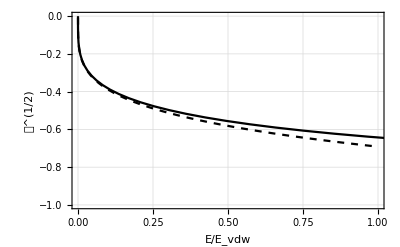

```mathematica
Show[Ahalfplot1,Ahalfplot2,Frame->True,LabelStyle->Large,GridLines->Automatic,FrameLabel->{"E/E_vdw","𝒜^(1/2)"},PlotRange->{{0,1},{-1,0}}]
```

```mathematica
Ahalffun=Interpolation[Ahalfdat,InterpolationOrder->1]
```

InterpolatingFunction[…]

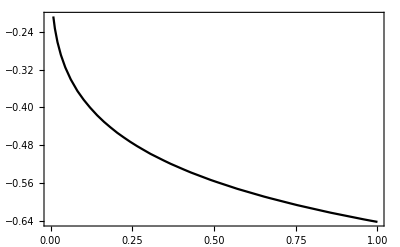

```mathematica
Plot[Ahalffun[ϵ],{ϵ,0.00001,1},Frame->True]
```

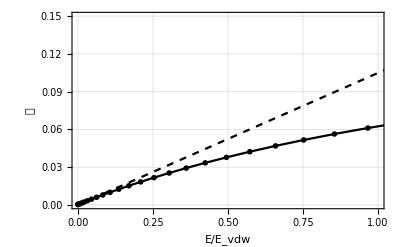

```mathematica
Gdat=Table[{ϵtable[[i]],lowEparameters[[i,3]]},{i,1,NE}];Gplot1=ListPlot[Gdat,PlotStyle->Black,Joined->True];
Gplot2=Plot[-ϵ/((2L+3)(2L-1))+(-1)^(L+1)(abar[ltest] √ϵ)^(4L+2)/.L->ltest,{ϵ,0,100},PlotStyle->{Black,Dashed}];
Show[Gplot1,Gplot2,Frame->True,PlotRange->{{0,1},{0,.15}},LabelStyle->Large,GridLines->Automatic,FrameLabel->{"E/E_vdw","𝒢"}]
```

```mathematica
Gfun=Interpolation[Gdat,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
ℰ[n_,Ecol_,B_]:=EthA[[1]][B]+Ecol-EthA[[n]][B]
```

```mathematica
Ecollision=1 nkinHartree Hartreeinvdw
```

1.722×10^-7

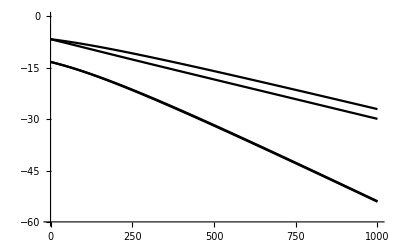

```mathematica
Plot[Table[ℰ[n,Ecollision,B],{n,2,5}],{B,0,1000},PlotRange->{-ϵtable[[NE]],-ϵtable[[1]]}]
```

```mathematica
cotγ=Interpolation[Table[{ϵ,Cot[γfun[ϵ]]},{ϵ,-ϵtable}],InterpolationOrder->1];
```

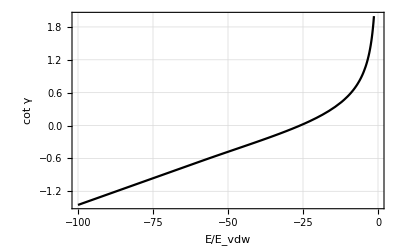

```mathematica
Plot[cotγ[ϵ],{ϵ,-100,-0.0001},Frame->True,FrameLabel->{"E/E_vdw","cot γ"},GridLines->Automatic,GridLinesStyle->Thin]
```

### Import the data from the full coupled-channels calculation using Johnson’s log-derivative method in FORTRAN

```mathematica
Li7FRData=Import["/Users/niravmehta/Documents/GitHub/LiScattering/Li7FR.dat"];
```

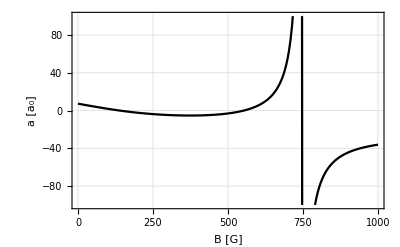

```mathematica
pexact50nk=ListPlot[Li7FRData,Joined->True,PlotMarkers->None,Frame->True,PlotRange->{-100,100},FrameLabel->{"B [G]","a [a_0]"},LabelStyle->Medium,GridLines->Automatic,GridLinesStyle->Thin]
```

### Calculate the singlet/triplet quantum defects and setup the MQDT parameters

```mathematica
μS[0]
μT[0]
```

-0.0311831

0.346357

```mathematica
KSRhf=FullSimplify[SymSingletProjLi7MF2*Tan[π μS[0]] + SymTripletProjLi7MF2*Tan[π μT[0]]]
```

{{1.40666,0.434438,0.354717,0.501645,-0.434438},{0.434438,1.53207,-0.307194,-0.434438,0.376234},{0.354717,-0.307194,1.65748,-0.354717,0.307194},{0.501645,-0.434438,-0.354717,1.40666,0.434438},{-0.434438,0.376234,0.307194,0.434438,1.53207}}

```mathematica
KSRrotated[B_]:=AsymC[B].KSRhf.Transpose[AsymC[B]];
MatrixForm[KSRrotated[0]]
```

(1.53207 | -0.307194 | 0.434438 | 0.376234 | -0.434438
-0.307194 | 1.65748 | 0.354717 | 0.307194 | -0.354717
0.434438 | 0.354717 | 1.40666 | -0.434438 | 0.501645
0.376234 | 0.307194 | -0.434438 | 1.53207 | 0.434438
-0.434438 | -0.354717 | 0.501645 | 0.434438 | 1.40666)

```mathematica
KQQ[B_]:=KSRrotated[B][[2;;5,2;;5]]
```

```mathematica
KPQ[B_]:=KSRrotated[B][[1,2;;5]]
```

```mathematica
KQP[B_]:=KSRrotated[B][[2;;5,1]]
```

```mathematica
KPP[B_]:=KSRrotated[B][[1,1]]
```

```mathematica
Ecollision=50 nkinHartree
```

1.58341×10^-13

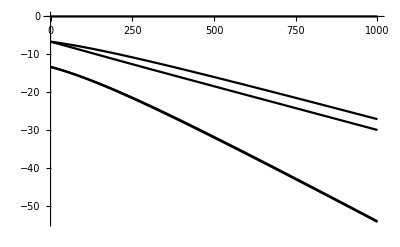

```mathematica
Btest=200.0;
Plot[Table[ℰ[n,Ecollision,B],{n,1,5}],{B,0.0,1000}]
```

```mathematica
DiagonalMatrix[Table[ cotγ[ℰ[n,ϵ,Btest]],{n,2,5}] ]
```

{{InterpolatingFunction[…][-9.80722+ϵ],0,0,0},{0,InterpolatingFunction[…][-11.3936+ϵ],0,0},{0,0,InterpolatingFunction[…][-19.4853+ϵ],0},{0,0,0,InterpolatingFunction[…][-19.6144+ϵ]}}

```mathematica
cotgammamatrix[ϵ_,B_]:=DiagonalMatrix[Table[cotγ[ℰ[n,ϵ,B]],{n,2,5}] ]
```

```mathematica
Ktilde[ϵ_,B_]:=KPP[B]-KPQ[B].(Inverse[KQQ[B]+cotgammamatrix[ϵ,B]]).KQP[B]
```

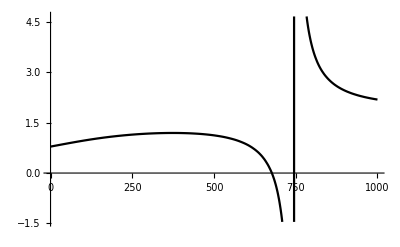

```mathematica
Plot[Ktilde[10^-10,B],{B,0,1000}]
```

```mathematica
Ecollision=0.01
```

0.01

```mathematica
KK[ϵ_,B_]:=Ahalffun[ℰ[1,ϵ,B]] 1/(Ktilde[ϵ,B]^-1+Gfun[ℰ[1,ϵ,B]])Ahalffun[ℰ[1,ϵ,B]]
```

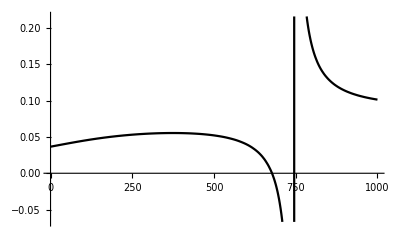

```mathematica
Plot[KK[Ecollision,B],{B,0,1000}]
```

```mathematica
Sphys[ϵ_,B_]:=Exp[ⅈ ηfun[ℰ[1,ϵ,B]]](1+ⅈ KK[ϵ,B])/(1-ⅈ KK[ϵ,B])Exp[ⅈ ηfun[ℰ[1,ϵ,B]]]
```

a=-(tan δ)/k=-1/(i k) (ⅇ^(i δ)-ⅇ^(-i δ))/(ⅇ^(i δ)+ⅇ^(-i δ))=-1/(i k) (ⅇ^(2i δ)-1)/(ⅇ^(2i δ)+1)=-1/(i k)(S-1)/(S+1)

a=-1/(i k)(S-1)/(S+1)=-1/(i k)(ⅇ^(i η)(1+i K)/(1-i K)ⅇ^(i η)-1)/(ⅇ^(i η)(1+i K)/(1-i K)ⅇ^(i η)+1)

a=-1/(i k)(S-1)/(S+1)=-1/(i k)(ⅇ^(i η)(1+i K)ⅇ^(i η)-1+i K)/(ⅇ^(i η)(1+i K)ⅇ^(i η)+1-i K)

a=-1/(i k)(S-1)/(S+1)=-1/(i k)(ⅇ^(i η)+i ⅇ^(i η) K-ⅇ^(-i η)+i ⅇ^(-i η)K)/(ⅇ^(i η)+i ⅇ^(i η)K+ⅇ^(-i η)-i ⅇ^(-i η) K)

a=-1/(i k)(S-1)/(S+1)=-1/(i k)(ⅇ^(i η)-ⅇ^(-i η)+i K (ⅇ^(i η) +ⅇ^(-i η)))/(ⅇ^(i η)+ⅇ^(-i η)+i K( ⅇ^(i η)- ⅇ^(-i η)))

a=-1/(i k)(S-1)/(S+1)=-1/(i k)(2i sin η+i K 2cos η)/(2cos η+i K 2 i sin η)

a=-1/(i k)(S-1)/(S+1)=-1/k(sin η+ K cos η)/(cos η- K sin η)

a=-1/(i k)(S-1)/(S+1)=-1/k(tan η+K)/(1- K tan η)

```mathematica
Tandel[ϵ_,B_]:=(Tan[ηfun[ϵ]]+KK[ϵ,B])/(1-KK[ϵ,B]Tan[ηfun[ϵ]])
```

```mathematica
kcotdel[ϵ_,B_]:=√ϵ(1-KK[ϵ,B]Tan[ηfun[ϵ]])/(Tan[ηfun[ϵ]]+KK[ϵ,B])
```

```mathematica
ascat[ϵ_,B_]:=-1/(√ϵ)(Tan[ηfun[ϵ]]+KK[ϵ,B])/(1-KK[ϵ,B]Tan[ηfun[ϵ]])(*Re[-1/(ⅈ √ϵ) (Sphys[ϵ,B]-1)/(Sphys[ϵ,B]+1)]*)
```

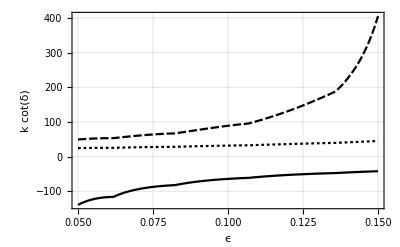

```mathematica
Btest = 200;pft=Plot[{-1/ascat[ϵ,150.0],-1/ascat[ϵ,200.0],-1/ascat[ϵ,250.0]},{ϵ,0.05,0.15},Frame->True,GridLines->Automatic,GridLinesStyle->Thin,FrameLabel->{"ϵ","k cot(δ)"}]
```

k cot δ = -1/a+1/2 r_e k^2+𝒪(k^4)

```mathematica
10^7 nkinHartree Hartreeinvdw
```

1.722

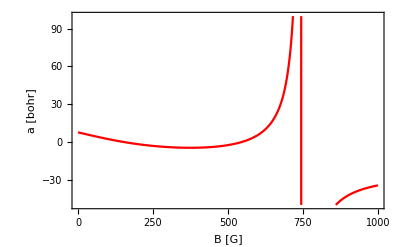

```mathematica
pft=ListPlot[Table[{B,βvdw ascat[.01,B]},{B,0,1000,1}],PlotRange->{-50,100},Frame->True,FrameLabel->{"B [G]","a [bohr]"},Joined->True,PlotMarkers->None,PlotStyle->Red]
```

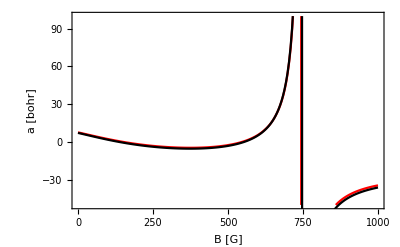

```mathematica
Show[pft,pexact50nk]
```

### Scattering Asymptotic Functions

```mathematica
se[l_,k_,r_]=√(k/π)r SphericalBesselJ[l,k r];
ce[l_,k_,r_]=-√(k/π)r SphericalBesselY[l,k r];
dse[l_,k_,r_]=Simplify[D[se[l,k,r],r]];
dce[l_,k_,r_]=Simplify[D[ce[l,k,r],r]];
```

```mathematica
Setupdiagsc[Ε_,Nopen_,Eth_,r_]:=Module[{ii},
s[Ε,r]=DiagonalMatrix[Table[se[0,√(2μ(Ε-Eth[[ii]])),r],{ii,1,Nopen}]];
c[Ε,r]=DiagonalMatrix[Table[ce[0,√(2μ(Ε-Eth[[ii]])),r],{ii,1,Nopen}]];
ds[Ε,r]=DiagonalMatrix[Table[dse[0,√(2μ(Ε-Eth[[ii]])),r],{ii,1,Nopen}]];
dc[Ε,r]=DiagonalMatrix[Table[dce[0,√(2μ(Ε-Eth[[ii]])),r],{ii,1,Nopen}]];
{s[Ε,r],c[Ε,r],ds[Ε,r],dc[Ε,r]}
]
```

```mathematica
Nchan = 5;
Btest=0.0;
eps = 10^-15;
Etest=Eth[Btest][[1]]+eps
√(2μ(Etest-Eth[Btest][[1]]))
NumOpen[Energy_,B_]:=Count[Eth[B],u_/;u<Energy]
no = NumOpen[Etest,Btest]
```

-8.30048

4.7664×10^-6

0

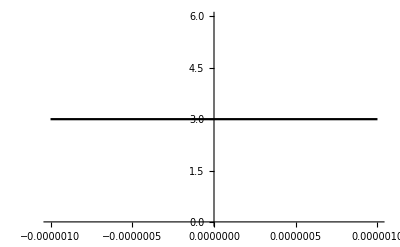

```mathematica
Plot[NumOpen[Energy,Btest],{Energy,-10^-6,10^-6}]
```